```mathematica
Assuming[rf∈Reals&&w >0,Mean[TransformedDistribution[Log[Exp[rf]+w*(Exp[r]-Exp[rf])],r\[Distributed]NormalDistribution[μ,σ]]]]
```

can I select out just the parameter dependencies? If so, could I just do this that way?

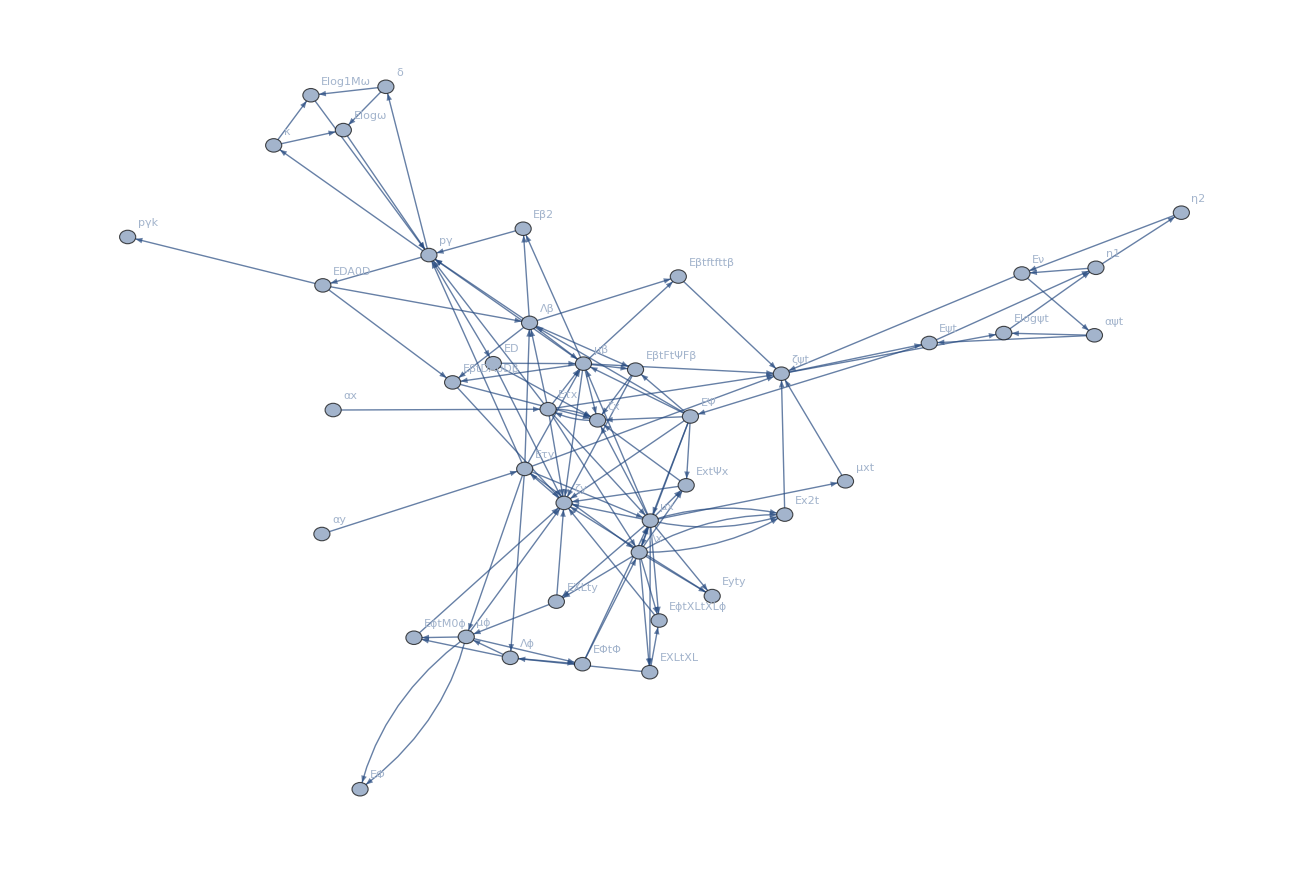

```mathematica
fg=Graph[{
EXLtXL->Λϕ,
Eτy->Λϕ,
EXLty->μϕ,
Eτy->μϕ,
Λϕ->μϕ,
EΦtΦ->Λx,
Eτy->Λx,
Eτx->Λx,
EΨ->Λx,
EΦtΦ->μx,
Eτy->μx,
Eτx->μx,
EΨ->μx,
Λx->μx,
Eyty->ζy,
EϕtXLtXLϕ->ζy,
EXLty->ζy,
μϕ->ζy,
EϕtM0ϕ->ζy,
ExtΨx->ζy,
EβtFtΨFβ->ζy,
EΨ->ζy,
μβ->ζy,
μx->ζy,
EβtDA0Dβ->ζy,
ED->ζy,
Eτx->ζy,
ExtΨx->ζx,
EβtFtΨFβ->ζx,
EΨ->ζx,
μβ->ζx,
μx->ζx,
EβtDA0Dβ->ζx,
ED->ζx,
Eτx->ζx,
EDA0D->Λβ,
EΨ->Λβ,
Eτx->Λβ,
Eτy->Λβ,
μx->μβ,
ED->μβ,
EΨ->μβ,
Eτx->μβ,
Eτy->μβ,
Λβ->μβ,
Eβ2->pγ,
Elog1Mω->pγ,
Elogω->pγ,
μβ->pγ,
Λβ->pγ,
EDA0D->pγk,
Eτx->pγ,
Eτy->pγ,
pγ->κ,
pγ->δ,
Eν->αψt,
Eν->ζψt,
Ex2t->ζψt,
μxt->ζψt,
Eβtftfttβ->ζψt,
μβ->ζψt,
Eτx->ζψt,
Eτy->ζψt,
Elogψt->η1,
Eψt->η1,
η1->η2,
μx -> EXLtXL,
Λx -> EXLtXL,
μx -> EXLty,
Λx -> EXLty,
αy->Eτy,
ζy->Eτy,
μϕ->EΦ,
μϕ->EΦtΦ,
Λϕ->EΦtΦ,
αx->Eτx,
ζx->Eτx,
αψt->Eψt,
ζψt->Eψt,
μx -> Eyty,
Λx -> Eyty,
EXLtXL->EϕtXLtXLϕ,
μx -> EϕtXLtXLϕ,
Λx -> EϕtXLtXLϕ,
μϕ->EϕtM0ϕ,
Λϕ->EϕtM0ϕ,
μx -> ExtΨx,
Λx -> ExtΨx,
EΨ-> ExtΨx,
μβ -> EβtFtΨFβ,
Λβ -> EβtFtΨFβ,
EΨ-> EβtFtΨFβ,
pγ->ED,
pγ->EDA0D,
μβ -> EβtDA0Dβ,
Λβ -> EβtDA0Dβ,
EDA0D-> EβtDA0Dβ,
μβ->Eβ2,
Λβ->Eβ2,
κ-> Elogω,
δ-> Elogω,
κ-> Elog1Mω,
δ-> Elog1Mω,
μx->Ex2t,
Λx->Ex2t,
μβ->Eβtftfttβ,
Λβ->Eβtftfttβ,
αψt->Elogψt,
ζψt->Elogψt,
η1->Eν,
η2->Eν,
μϕ->EΦ,
μx->μxt,
μx->Ex2t,
Λx->Ex2t,
Eψt->EΨ

},VertexLabels->"Name"]
```

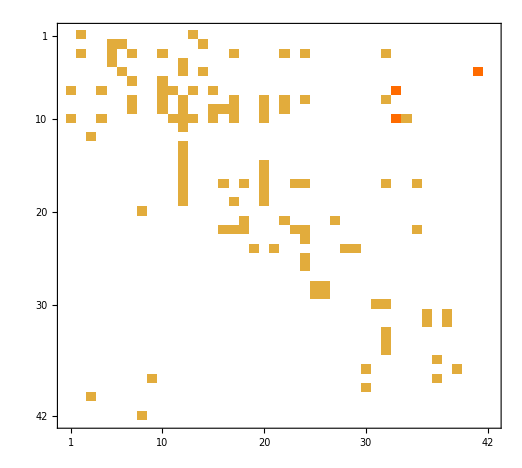

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[SparseArray[Automatic,{42,42},0,{1,{{0,2,5,13,15,19,21,28,36,44,54,55,56,57,58,60,62,70,72,75,76,79,85,86,90,91,92,92,94,96,98,100,102,103,104,105,106,108,110,111,112,112,113},{{2},{13},{5},{6},{14},{2},{5},{7},{10},{17},{22},{24},{32},{5},{12},{6},{12},{14},{41},{7},{10},{1},{4},{10},{11},{13},{15},{33},{7},{10},{12},{17},{20},{22},{24},{32},{7},{10},{12},{15},{16},{17},{20},{22},{1},{4},{11},{12},{13},{15},{17},{20},{33},{34},{12},{3},{12},{12},{12},{20},{12},{20},{12},{16},{18},{20},{23},{24},{32},{35},{12},{20},{12},{17},{20},{8},{18},{22},{27},{16},{17},{18},{23},{24},{35},{24},{19},{21},{28},{29},{24},{24},{25},{26},{25},{26},{31},{32},{36},{38},{36},{38},{32},{32},{32},{37},{30},{39},{9},{37},{30},{3},{8}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}]]

```mathematica
MatrixPlot[AdjacencyMatrix[fg]]
```